```mathematica
Needs["PacletManager`"]
```

```mathematica
PacletInstall["~/Downloads/MaTeX-1.7.8.paclet"]
```

PacletObject[…]

```mathematica
<<MaTeX`
```

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{mathtext}" ,
"\\usepackage[T2A]{fontenc}",
"\\usepackage[utf8]{inputenc}",
"\\usepackage[english,russian]{babel}"}];
```

```mathematica
functions={x,x^2}
```

{x,x^2}

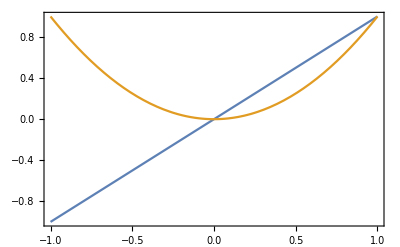

```mathematica
Plot[functions,{x,-1,1},Frame->True,BaseStyle->{FontFamily->"CMU Serif"},PlotLegends->MaTeX@functions,FrameLabel->MaTeX@{"\\text{аргумент } x","\\text{функция }f(x)"}]
```